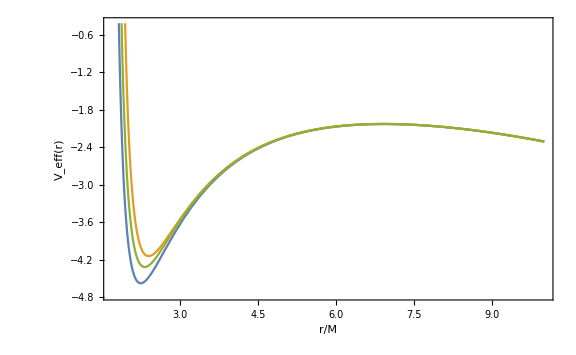

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
Veff[r_,L_,Ene_,ω_,Ω_,γ_] = -1 + Ene^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2; (*ω = eB/(2mc)*)
Plot[{Veff[r,6,1,0.1,0.6,0.1],Veff[r,6,1,0.1,0.4,0.4],Veff[r,6,1,0.1,0.4,0.8]},{r,1.7,10},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = 0.1, Ω = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large]
```